## Задание 1.

Спроектируйте и создайте функции для построения выпуклой оболочки заданного множества точек плоскости с использованием алгоритма Джарвиса . Проведите тестирование .

```mathematica
ClearAll[NamedQ,𝔨𝔪];
(** Атрибуты и описание **)
𝔨𝔪::usage="Knowledge base «computer mathematics»";
SetAttributes[𝔨𝔪,{Protected,ReadProtected}];
NamedQ::usage="Check: is there a name of tested equations";
NamedQ[n1_,n2__]:=And[NamedQ[n1],NamedQ[n2]];
SetAttributes[NamedQ,Listable];
```

```mathematica
ClearAll[kmPoint];
(** Атрибуты и описание **)
SetAttributes[kmPoint,ReadProtected];
kmPoint::usage="Point on the surface";
(** Свойства **)
NamedQ[kmPoint[𝔨𝔪,id_String,___]]^:=id≠"";
kmPoint[𝔨𝔪,_String,coord_List,___]["coord"]:=coord;
kmPoint[𝔨𝔪,id_String,___]["id"]:=If[id=="","Point",id];
(** Конструкторы **)
kmPoint[id_String,coord:{_,_}]:=kmPoint[𝔨𝔪,id,coord];
kmPoint[coord:{_,_}]:=kmPoint[𝔨𝔪,"",coord];
kmPoint[{L1_kmLine,L2_kmLine}]:=kmPoint[#[[2]]&/@(First@NSolve@Through[{L1,L2}@"equ"])]
(** Декораторы **)
Format[P_kmPoint,StandardForm]:=Row@{P["id"],"(",Row[P["coord"],","],")"};
```

```mathematica
ClearAll[kmVector];
(** Атрибуты и описание **)
SetAttributes[kmVector,ReadProtected];
kmVector::usage="Vector on the surface";
(** Свойства **)
NamedQ[kmVector[𝔨𝔪,id_String,___]]^:=id≠"";
kmVector[𝔨𝔪,id_String,___]["id"]:=If[id=="","Vector",id];
kmVector[𝔨𝔪,_String,coord_List,___]["coord"]:=coord;
kmVector[𝔨𝔪,_String,coord_List,___]["norm"]:=Sqrt[Plus@@(coord*coord)];
(** Конструкторы **)
kmVector[id_String,coord_List]:=kmVector[𝔨𝔪,id,coord];
kmVector[coord_List]:=kmVector[𝔨𝔪,"",coord];
kmVector[id_String,P0_kmPoint,P1_kmPoint]:=kmVector[id,P1@"coord"-P0@"coord"];
kmVector[P0_kmPoint,P1_kmPoint]:=kmVector[
If[NamedQ[P0,P1],StringJoin[P0@"id",P1@"id"],""],P0,P1];
(** Декораторы **)
MakeBoxes[V_kmVector,StandardForm]^:=TemplateBox[{V@"id",
RowBox@Riffle[MakeBoxes[#,StandardForm]&/@V["coord"],","]
},"Point2D",
DisplayFunction:>(RowBox@{OverscriptBox[#1,"⇀"],"(",#2,")"}&),
InterpretationFunction->(RowBox@{"{",#2,"}"}&),
Tooltip->Automatic];
```

```mathematica
Q=kmPoint[{RandomReal[{-10,10}],RandomReal[{-10,10}]}]&/@Range[20]
```

{Point(,,-9.95255.38208),Point(,,-9.619787.94961),Point(,,-3.399279.26892),Point(,,2.288549.83829),Point(,,-0.977853-7.58629),Point(,,1.550763.23231),Point(,,0.3970033.27646),Point(,,0.6519088.52106),Point(,,4.5634-9.53463),Point(,,-6.036263.18315),Point(,,-7.211278.98308),Point(,,-1.856780.723011),Point(,,3.480122.18548),Point(,,6.87816-4.70371),Point(,,-9.93689-0.15463),Point(,,-2.66167-7.58358),Point(,,3.75731-8.07247),Point(,,1.068082.75411),Point(,,6.771982.67514),Point(,,4.062094.03511)}

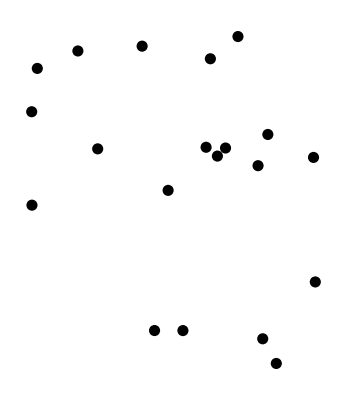

```mathematica
pointsPicture=Graphics[{PointSize@0.02,Point[#["coord"]]&/@Q}]
```

```mathematica
StartPoint=Q[[1]]
```

Point(,,-9.95255.38208)

```mathematica
For[
i=2,i<=Length@Q,i++,
If[
And[
Or[
Q[[i]]["coord"][[2]]<StartPoint["coord"][[2]],
Q[[i]]["coord"][[2]]==StartPoint["coord"][[2]]
],
Q[[i]]["coord"][[1]]<StartPoint["coord"][[1]]
],
StartPoint=Q[[i]]
]
]
```

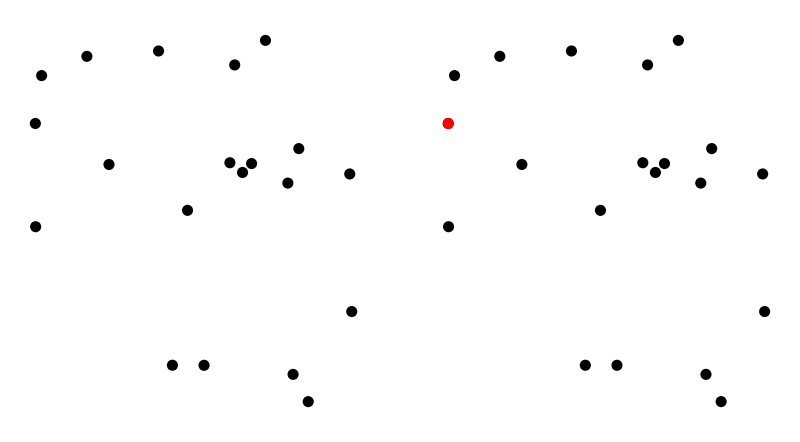

```mathematica
pointsPictureWithStartPoint=Graphics[{PointSize@0.02,Point[#["coord"]]&/@Q,Red,Point@StartPoint["coord"]}];
GraphicsRow[{pointsPicture,pointsPictureWithStartPoint},Frame->All]
```

```mathematica
L={StartPoint};
NextPoint=First@Q
CurrentPoint=Last[L]
```

Point(,,-9.95255.38208)

Point(,,-9.95255.38208)

```mathematica
getTriangleAlgebraicSquare[points_List]:=Module[{a=points[[1]]["coord"],b=points[[2]]["coord"],c=points[[3]]["coord"]},1/2 Det[{b-a,c-a}]]
```

```mathematica
isPointOnLine[Line_kmLine,P_kmPoint]:=Line["equ"]/.{x->P["coord"][[1]],y->P["coord"][[2]]}
```

```mathematica
Unprotect[Unequal];
```

```mathematica
Unequal[Point1_kmPoint,Point2_kmPoint]:=Point1["coord"]!=Point2["coord"]
```

Важно закинуть стартовую точку в конец Q.

```mathematica
getStartPoint[Q_List]:=Module[{StartPoint=Q[[1]]},
For[
i=2,i<=Length@Q,i++,
If[
And[
Or[
Q[[i]]["coord"][[2]]<StartPoint["coord"][[2]],
Q[[i]]["coord"][[2]]==StartPoint["coord"][[2]]
],
Q[[i]]["coord"][[1]]<StartPoint["coord"][[1]]
],
StartPoint=Q[[i]]
]
];
Return@StartPoint
]
```

```mathematica
moveToEndOfList[lst_List,obj_]:=Append[DeleteCases[lst,obj],obj]
```

```mathematica
Q=kmPoint[{RandomReal[{-10,10}],RandomReal[{-10,10}]}]&/@Range[20]
```

{Point(,,8.75925-8.06671),Point(,,8.07603-9.09465),Point(,,-6.605743.17983),Point(,,4.97015-6.31474),Point(,,-7.6181-7.68454),Point(,,-0.08895774.44258),Point(,,9.93171-4.19448),Point(,,1.47991-4.85747),Point(,,1.563849.16124),Point(,,3.59732-1.12969),Point(,,-4.55873.58264),Point(,,-3.43376-5.79902),Point(,,-9.72838-8.31405),Point(,,8.036486.90938),Point(,,-5.34861.49128),Point(,,-6.662117.93529),Point(,,8.660867.15803),Point(,,1.1002-5.21936),Point(,,-1.36509-1.9479),Point(,,-4.9629-9.23454)}

```mathematica
CH[pointsList_List]:=Module[{i=1,Q=pointsList,StartPoint,CurrentPoint,NextPoint,algebraicSquare,L={}},
StartPoint=getStartPoint[Q];
L=AppendTo[L,StartPoint];
Q=moveToEndOfList[Q,StartPoint];
CurrentPoint=StartPoint;
NextPoint=Q[[1]];
While[
NextPoint!=StartPoint,
Do[
algebraicSquare=getTriangleAlgebraicSquare[{CurrentPoint,NextPoint,i}];
If[algebraicSquare>0,NextPoint=i],
{i,Q}
];
Q=DeleteCases[Q,NextPoint];
L=AppendTo[L,NextPoint];
CurrentPoint=NextPoint;
NextPoint=Q[[1]]
];
Return@L
]
```

```mathematica
CH[Q]
```

Q {Point(,,8.75925-8.06671),Point(,,8.07603-9.09465),Point(,,-6.605743.17983),Point(,,4.97015-6.31474),Point(,,-7.6181-7.68454),Point(,,-0.08895774.44258),Point(,,9.93171-4.19448),Point(,,1.47991-4.85747),Point(,,1.563849.16124),Point(,,3.59732-1.12969),Point(,,-4.55873.58264),Point(,,-3.43376-5.79902),Point(,,-9.72838-8.31405),Point(,,8.036486.90938),Point(,,-5.34861.49128),Point(,,-6.662117.93529),Point(,,8.660867.15803),Point(,,1.1002-5.21936),Point(,,-1.36509-1.9479),Point(,,-4.9629-9.23454)}

NextPointPoint(,,-9.72838-8.31405)

Q without nextPoint{Point(,,8.75925-8.06671),Point(,,8.07603-9.09465),Point(,,-6.605743.17983),Point(,,4.97015-6.31474),Point(,,-7.6181-7.68454),Point(,,-0.08895774.44258),Point(,,9.93171-4.19448),Point(,,1.47991-4.85747),Point(,,1.563849.16124),Point(,,3.59732-1.12969),Point(,,-4.55873.58264),Point(,,-3.43376-5.79902),Point(,,8.036486.90938),Point(,,-5.34861.49128),Point(,,-6.662117.93529),Point(,,8.660867.15803),Point(,,1.1002-5.21936),Point(,,-1.36509-1.9479),Point(,,-4.9629-9.23454)}

L{Point(,,-4.9629-9.23454),Point(,,-9.72838-8.31405)}

new currentPointPoint(,,-9.72838-8.31405)

new NextPointPoint(,,8.75925-8.06671)

Q {Point(,,8.75925-8.06671),Point(,,8.07603-9.09465),Point(,,-6.605743.17983),Point(,,4.97015-6.31474),Point(,,-7.6181-7.68454),Point(,,-0.08895774.44258),Point(,,9.93171-4.19448),Point(,,1.47991-4.85747),Point(,,1.563849.16124),Point(,,3.59732-1.12969),Point(,,-4.55873.58264),Point(,,-3.43376-5.79902),Point(,,8.036486.90938),Point(,,-5.34861.49128),Point(,,-6.662117.93529),Point(,,8.660867.15803),Point(,,1.1002-5.21936),Point(,,-1.36509-1.9479),Point(,,-4.9629-9.23454)}

NextPointPoint(,,-6.662117.93529)

Q without nextPoint{Point(,,8.75925-8.06671),Point(,,8.07603-9.09465),Point(,,-6.605743.17983),Point(,,4.97015-6.31474),Point(,,-7.6181-7.68454),Point(,,-0.08895774.44258),Point(,,9.93171-4.19448),Point(,,1.47991-4.85747),Point(,,1.563849.16124),Point(,,3.59732-1.12969),Point(,,-4.55873.58264),Point(,,-3.43376-5.79902),Point(,,8.036486.90938),Point(,,-5.34861.49128),Point(,,8.660867.15803),Point(,,1.1002-5.21936),Point(,,-1.36509-1.9479),Point(,,-4.9629-9.23454)}

L{Point(,,-4.9629-9.23454),Point(,,-9.72838-8.31405),Point(,,-6.662117.93529)}

new currentPointPoint(,,-6.662117.93529)

new NextPointPoint(,,8.75925-8.06671)

Q {Point(,,8.75925-8.06671),Point(,,8.07603-9.09465),Point(,,-6.605743.17983),Point(,,4.97015-6.31474),Point(,,-7.6181-7.68454),Point(,,-0.08895774.44258),Point(,,9.93171-4.19448),Point(,,1.47991-4.85747),Point(,,1.563849.16124),Point(,,3.59732-1.12969),Point(,,-4.55873.58264),Point(,,-3.43376-5.79902),Point(,,8.036486.90938),Point(,,-5.34861.49128),Point(,,8.660867.15803),Point(,,1.1002-5.21936),Point(,,-1.36509-1.9479),Point(,,-4.9629-9.23454)}

NextPointPoint(,,1.563849.16124)

Q without nextPoint{Point(,,8.75925-8.06671),Point(,,8.07603-9.09465),Point(,,-6.605743.17983),Point(,,4.97015-6.31474),Point(,,-7.6181-7.68454),Point(,,-0.08895774.44258),Point(,,9.93171-4.19448),Point(,,1.47991-4.85747),Point(,,3.59732-1.12969),Point(,,-4.55873.58264),Point(,,-3.43376-5.79902),Point(,,8.036486.90938),Point(,,-5.34861.49128),Point(,,8.660867.15803),Point(,,1.1002-5.21936),Point(,,-1.36509-1.9479),Point(,,-4.9629-9.23454)}

L{Point(,,-4.9629-9.23454),Point(,,-9.72838-8.31405),Point(,,-6.662117.93529),Point(,,1.563849.16124)}

new currentPointPoint(,,1.563849.16124)

new NextPointPoint(,,8.75925-8.06671)

```mathematica
Q
```

{Point(,,8.75925-8.06671),Point(,,8.07603-9.09465),Point(,,-6.605743.17983),Point(,,4.97015-6.31474),Point(,,-7.6181-7.68454),Point(,,-0.08895774.44258),Point(,,9.93171-4.19448),Point(,,1.47991-4.85747),Point(,,1.563849.16124),Point(,,3.59732-1.12969),Point(,,-4.55873.58264),Point(,,-3.43376-5.79902),Point(,,-9.72838-8.31405),Point(,,8.036486.90938),Point(,,-5.34861.49128),Point(,,-6.662117.93529),Point(,,8.660867.15803),Point(,,1.1002-5.21936),Point(,,-1.36509-1.9479),Point(,,-4.9629-9.23454)}

```mathematica
CurrentPoint=StartPoint;
NextPoint=Q[[1]];
While[
CurrentPoint!=NextPoint,
Do[
algebraicSquare=getTriangleAlgebraicSquare[{CurrentPoint,NextPoint,i}];
If[algebraicSquare>0,NextPoint=i],
{i,Q}
];
Q=DeleteCases[Q,NextPoint];
L=AppendTo[L,NextPoint];
CurrentPoint=NextPoint;
NextPoint=Q[[1]]
];
Return@L
```

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

Det::luc: Result for Det of badly conditioned matrix {{5.23997,2.91947},{5.23997,2.91947}} may contain significant numerical errors.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of $IterationLimit::itlim will be suppressed during this calculation.

Det::luc: Result for Det of badly conditioned matrix {{7.78546,-9.60457},{7.78546,-9.60457}} may contain significant numerical errors.

Det::luc: Result for Det of badly conditioned matrix {{5.17684,-9.89473},{5.17684,-9.89473}} may contain significant numerical errors.

General::stop: Further output of Det::luc will be suppressed during this calculation.

Return[{Point(,,-9.95255.38208),Point(,,-4.712528.30155),Point(,,-2.10398.59172),Point(,,8.325377.10262),Point(,,9.93683-2.15378),Point(,,7.38258-6.72619),Point(,,-3.89553-8.44986),Point(,,-6.24568-3.48917),Point(,,-8.108012.36448),Point(,,-2.763788.47765),Point(,,-1.737458.23308),Point(,,2.027345.7828),Point(,,9.465910.0400651),Point(,,6.05723-4.95824),Point(,,-5.423963.22018),Point(,,-1.694422.54839),Point(,,8.45709-1.2916),Point(,,3.07294-1.30301),Point(,,5.83341-0.672829)}]

```mathematica
aTest={1,2,3,4,5,6,7,8,9,10}
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
aTest=DeleteCases[aTest,1]
```

{2,3,4,5,6,7,8,9,10}

```mathematica
aTest
```

{2,3,4,5,6,7,8,9,10}